```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
alpha[r_,k_,l_,h_]:=(1+h (D[FunctionExpand[RiccatiBesselN[k x,l]],x]/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
beta[r_,k_,l_,h_]:=h FunctionExpand[RiccatiBesselJ[k r,l]](((D[FunctionExpand[RiccatiBesselJ[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselJ[k r,l]])-((D[FunctionExpand[RiccatiBesselN[k x,l]],x])/.x->r)/(FunctionExpand[RiccatiBesselN[k r,l]]))
```

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a0_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol},

hDif=Rdis/Npoints;


Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-mh2 Vloc[i hDif,lam,c0,d0,a0]-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
Wmat=Table[-hDif^3 mh2 Wnoloc[i hDif,j hDif,momentum^2/(2 μ),lam,c0,d0,a0,Lin],{i,1,Npoints},{j,1,Npoints}]; 

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

Amat=Dmat+Kmat+Wmat;

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

wf=Table[{i hDif,usol⟦i⟧},{i,1,Npoints}];
tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

```mathematica
(* Nuclear E2=2.22 E3=8.48 *)
LEC={(*{0.16,1,-5.23609711,-0.2508527567},{0.2,1,-6.21155090,-0.01411577035},{0.3,1,-9.04089890,0.9058334635},{0.35,1,-10.66481819,1.562725218},{0.4,1,-12.42824554,2.36543082},{0.45,1,-14.33104515,3.3244409},{0.5,1,-16.37322998,4.450396189},{0.55,1,-18.55475197,5.753778748},{0.6,1,-20.87557983,7.245120228},{0.65,1,-23.33569527,8.935015304},{0.7,1,-25.93508911,10.83416803},{0.75,1,-28.67371368,12.95315533},{0.8,1,-31.55156555,15.30282946},{0.85,1,-34.56868362,17.89442822},{0.9,1,-37.72501221,20.7388847},{0.95,1,-41.02048416,23.84721094},*)
{1.00,1,-44.45520020,27.2312836},
{1.05,1,-48.02915573,30.9028667},
{1.10,1,-51.74223328,34.8734185},
{1.20,1,-59.58599854,43.7610139},
{1.50,1,-86.45745087,78.9169705},
{2.00,1,-142.3761444,172.703829},
{3.00,1,-295.9593505,559.013463},
{4.00,1,-505.2016601,1397.56945},
{6.00,1,-1090.6288,2654.5400},
{10.0,1,-2933.5564,21297.6851},
{14.0,1,-5676.2972,144399.039}};
(*{6.00,1,-1090.661132,6311.30367},*)
(*{10.0,1,-2929.476318,89436.1852}};*)
```

```mathematica
Vc[r_,lam_,Cc_]:=Cc Exp[-lam r^2];

Vloc[r_,lam_,Cc_,Dd_,Aa_]:=2 Cc (3 Aa/(3 Aa+lam))^(3/2) Exp[-(3 Aa lam/(3 Aa+lam)) r^2]+8 Dd (3 Aa^2/(12 Aa^2+16 Aa lam+lam^2))^(3/2) Exp[-(12 Aa lam (Aa+lam)/(12 Aa^2+16 Aa lam+lam^2)) r^2];

Wnoloc[r_,rp_,e_,lam_,Cc_,Dd_,Aa_,Ll_]:=-(4 Pi r rp) (

27/8 (3/2 Aa)^(3/2) 1/mh2 Exp[-(15/16) Aa (r^2+rp^2)] ((-(4 (Aa 15/16)^2 r^2+(Aa 15/16)^2 rp^2-2 (Aa 15/16))+(Ll+1) Ll/r^2-mh2 e) I^Ll  SphericalBesselJ[Ll,I (Aa 18/16) r rp]
-4 (Aa 15/16) (Aa 18/16) r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I (Aa 18/16) r rp],{l,-Ll,Ll}]
)

-I^Ll 2 27 (3/2 Aa)^(3/2) Cc (Aa/(4 Aa+lam))^(3/2) SphericalBesselJ[Ll,I (9 Aa (Aa+lam))/(2 (4 Aa+lam)) r rp] Exp[-(3 Aa (5 Aa+8 lam))/(4 (4 Aa+lam)) r^2-(3 Aa (5 Aa+2 lam))/(4 (4 Aa+lam)) rp^2]

-I^Ll 27 (3/2 Aa)^(3/2) Dd (Aa/(4 Aa+5 lam))^(3/2) SphericalBesselJ[Ll,I (9 (4 Aa^2+8 Aa lam+3 lam^2))/(2 (16 Aa+20 lam)) r rp] Exp[-(3 (20 Aa^2+52 Aa lam+27 lam^2))/(4 (16 Aa+20 lam)) r^2-(3 (20 Aa^2+28 Aa lam+3 lam^2))/(4 (16 Aa+20 lam)) rp^2]
);
```

scattering length

a_l=-(tan δ_l(k))/k^(2l+1)

```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
```

(1-3) neutron-triton S-wave scattering length -- used to calibrate α

we chose the singlet n-t value a_s≈9±2fm to ensure that the naive estimate for the α parameter of the triton is not unreasonable

```mathematica
nGrid     =400;

ErangeMeV=Range[0.01,3,0.5];
PrangeFM=(Sqrt[2 μ #]/hbar)&/@ErangeMeV;

aff=5.;
hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;
```

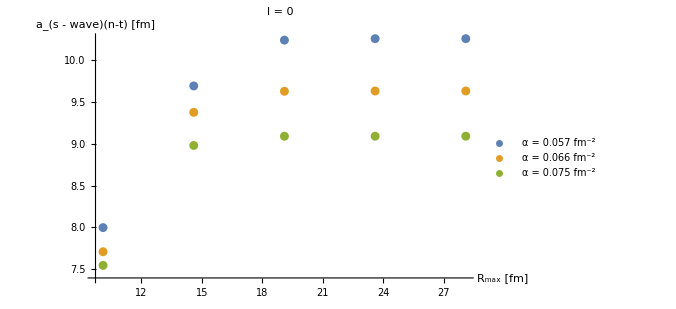

```mathematica
Lrel=0;
aOfa={};
αRange=Subdivide[0.95 3/2 aff^(-2),1.25 3/2 aff^(-2),2];
Do[
SetSharedVariable[aS];
aS={};
nn=Length[LEC]-2;
ParallelDo[
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];
mom=0.0001;
TanDelSwave=Chop[SolveSecular[rr,nGrid,mom,0,λ,C0,D0,α0]];
AppendTo[aS,{rr,-TanDelSwave/mom^(2 Lrel+1)}];
,{rr,Range[10.1,30.1,4.5]}];
a0=Reverse[Sort[aS,#1[[1]]>#2[[1]]&]];
AppendTo[aOfa,a0];
,{α0,αRange}];
leg="α = "<>ToString[#]<>" fm^-2"&/@αRange;
ListPlot[aOfa,AxesLabel->{"R_max [fm]","a_(s - wave)(n-t) [fm]"},ImageSize->500,PlotLegends->leg,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
```

α-fitting for different cutoffs

```mathematica
nGrid=150;
Lrel=0;
rr=20;
mom=0.001;
afit=(-mom)10;
aini=3/2 aff^(-2);
Do[
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];
alfL=FindRoot[Chop[SolveSecular[rr,nGrid,mom,Lrel,λ,C0,D0,alf]]==afit,{alf,1.1 aini},AccuracyGoal->6,PrecisionGoal->6];
Print["λ = ",λ," : ",alfL];
,{nn,Range[Length[LEC]]}];
```

λ = 0.25 : {alf→0.0662954+6.99881×10^-18 ⅈ}

$Aborted

(1-3) neutron-triton (S-wave)

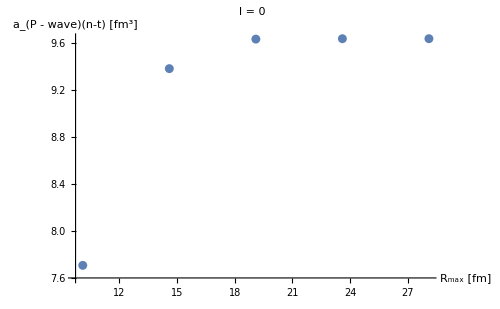

```mathematica
nGrid     =250;
ErangeMeV=(*{0.001};*)Range[0.01,3,0.5];
PrangeFM=(Sqrt[2 μ #]/hbar)&/@ErangeMeV;
Lrel=0;
a0fa={};
α0=0.066;
mom=0.001;
SetSharedVariable[aS];
aS={};
nn=Length[LEC]-2;
ParallelDo[
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,mom,Lrel,λ,C0,D0,α0]];
AppendTo[aS,{rr,-TanDelPwave/mom^(2 Lrel+1)}];
,{rr,Range[10.1,30.1,4.5]}];
a0=Reverse[Sort[aS,#1[[1]]>#2[[1]]&]];
AppendTo[a0fa,a0];

leg="α = "<>ToString[#]<>" fm^-2"&/@α0;
ListPlot[a0fa,AxesLabel->{"R_max [fm]","a_(P - wave)(n-t) [fm^3]"},ImageSize->500,PlotLegends->leg,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
```

S-matrix pole (S-wave)

Kukulin, Theory of Resonances, ch.6.1.1 Eq.(1.1) ff      S_l(k)=Numerator/(k^(2l+1)cotδ_l-ik^(2l+1))      →_(k→0)        Numerator/(-a_l^-1+1/2 r_l k^2+O(k^4)-ik^(2l+1))
Pade (typeII): X_l(k)=(P_N^(l)(k^2))/(Q_M^(l)(k^2)):=k^(2l+1)cotδ_l  ⇒   S_l(k)=(P_N^(l)(k^2) + ik^(2l+1)Q_M^(l)(k^2))/(P_N^(l)(k^2) - ik^(2l+1)Q_M^(l)(k^2))    ⇒     P_N^(l)(k_res^2)-ik_res^(2l+1)Q_M^(l)(k_res^2)=0

```mathematica
nGrid     =250;
ErangeMeV=(*{0.001};*)Range[0.01,3,0.5];
PrangeFM=(Sqrt[2 μ #]/hbar)&/@ErangeMeV;
Lrel=0;

α0=0.066;

Poles={};PadeSolus={};data={};
Do[
SetSharedVariable[Xl];
Xl={};
rr=20;
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];
ParallelDo[
TanDel=Chop[SolveSecular[rr,nGrid,mom,Lrel,λ,C0,D0,α0]];
AppendTo[Xl,{mom,(mom^(2 Lrel+1))/TanDel}];
,{mom,PrangeFM}];
Xlr=Reverse[Sort[Xl,#1[[1]]>#2[[1]]&]];
AppendTo[data,Xlr];

PadeOrderN=3;PadeOrderM=3;
coffs={Array[cn,PadeOrderN+1],Array[cm,PadeOrderM+1]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{-10.01,10.2},Length[Flatten[coffs]]]}];
constr=10^2>#>-10^2&/@Flatten[coffs];

PadePolyP=Sum[coffs[[1]][[i+1]] k^(2 i),{i,0,PadeOrderN}];
PadePolyQ=Sum[coffs[[2]][[i+1]] k^(2 i),{i,0,PadeOrderM}];
modelX=PadePolyP/PadePolyQ;

solu=FindFit[Xlr,{modelX,constr},Flatten[coffs],k];
pole=FindRoot[(PadePolyP-I k^(2 Lrel+1) PadePolyQ)/.solu,{k,2.1-0.98 I}];
Print["λ = ",λ,"   : k_pole = ",pole,"   ",solu];
AppendTo[Poles,{λ,pole}];
AppendTo[PadeSolus,{λ,solu}];
,{nn,Range[Length[LEC]]}]
```

λ = 0.25   : k_pole = {k→0.306064+0.177881 ⅈ}   {cn[1]→-0.0125364,cn[2]→0.535544,cn[3]→-1.45472,cn[4]→0.615903,cm[1]→0.125374,cm[2]→-1.19463,cm[3]→-0.0559037,cm[4]→0.772519}

λ = 0.275625   : k_pole = {k→0.30478+0.175191 ⅈ}   {cn[1]→-0.00804849,cn[2]→0.345449,cn[3]→-1.02438,cn[4]→0.675218,cm[1]→0.0804161,cm[2]→-0.783452,cm[3]→0.119455,cm[4]→0.804217}

λ = 0.3025   : k_pole = {k→0.305446+0.178914 ⅈ}   {cn[1]→-0.0116037,cn[2]→0.494131,cn[3]→-1.34353,cn[4]→0.61675,cm[1]→0.115893,cm[2]→-1.10179,cm[3]→-0.0198607,cm[4]→0.77318}

λ = 0.36   : k_pole = {k→0.304257+0.176923 ⅈ}   {cn[1]→-0.00736859,cn[2]→0.315477,cn[3]→-0.953398,cn[4]→0.665716,cm[1]→0.0735043,cm[2]→-0.719188,cm[3]→0.176106,cm[4]→0.807905}

λ = 0.5625   : k_pole = {k→0.303966+0.181165 ⅈ}   {cn[1]→-0.00804966,cn[2]→0.341761,cn[3]→-0.991306,cn[4]→0.604792,cm[1]→0.0801358,cm[2]→-0.773226,cm[3]→0.162456,cm[4]→0.781443}

λ = 1.   : k_pole = {k→0.303736+0.183958 ⅈ}   {cn[1]→-0.0167702,cn[2]→0.698657,cn[3]→-1.67708,cn[4]→0.656017,cm[1]→0.166549,cm[2]→-1.51175,cm[3]→-0.308097,cm[4]→0.74715}

λ = 2.25   : k_pole = {k→0.302343+0.185525 ⅈ}   {cn[1]→-0.0122626,cn[2]→0.506963,cn[3]→-1.25784,cn[4]→0.678109,cm[1]→0.121254,cm[2]→-1.10182,cm[3]→-0.0735393,cm[4]→0.777078}

λ = 4.   : k_pole = {k→0.301481+0.190394 ⅈ}   {cn[1]→-0.0100457,cn[2]→0.411706,cn[3]→-1.0615,cn[4]→0.598736,cm[1]→0.0988218,cm[2]→-0.904005,cm[3]→0.112097,cm[4]→0.767624}

λ = 9.   : k_pole = {k→1.11483-0.0607199 ⅈ}   {cn[1]→-0.0138178,cn[2]→0.536361,cn[3]→-1.14241,cn[4]→0.746269,cm[1]→0.132933,cm[2]→-1.11609,cm[3]→-0.186583,cm[4]→0.768772}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

λ = 25.   : k_pole = {k→0.230984-0.00812629 ⅈ}   {cn[1]→0.000718734,cn[2]→-0.0220844,cn[3]→0.101975,cn[4]→0.904478,cm[1]→0.00747221,cm[2]→-0.233329,cm[3]→1.7153,cm[4]→1.11802}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

λ = 49.   : k_pole = {k→0.401405+0.0658398 ⅈ}   {cn[1]→-0.00184464,cn[2]→0.0947601,cn[3]→-0.659156,cn[4]→0.681135,cm[1]→0.0189287,cm[2]→-0.292672,cm[3]→0.747209,cm[4]→0.933106}

{{0.25,0.306064+0.177881 ⅈ},{0.275625,0.30478+0.175191 ⅈ},{0.3025,0.305446+0.178914 ⅈ},{0.36,0.304257+0.176923 ⅈ},{0.5625,0.303966+0.181165 ⅈ},{1.,0.303736+0.183958 ⅈ},{2.25,0.302343+0.185525 ⅈ},{4.,0.301481+0.190394 ⅈ},{9.,1.11483-0.0607199 ⅈ},{25.,0.230984-0.00812629 ⅈ},{49.,0.401405+0.0658398 ⅈ}}

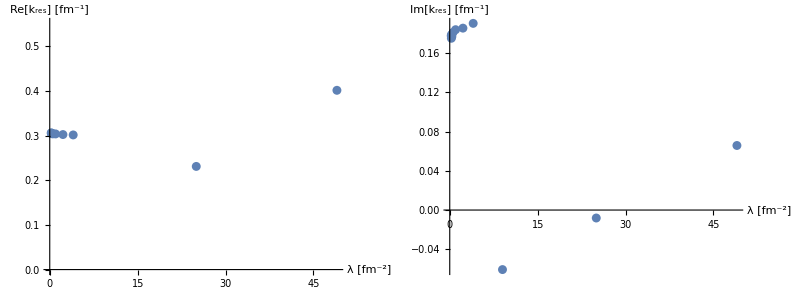

```mathematica
Poland=Transpose[{Poles[[All,1]],k/.Poles[[All,2]]}]
PolandRe=Transpose[{Poles[[All,1]],Re[k/.Poles[[All,2]]]}];
PolandIm=Transpose[{Poles[[All,1]],Im[k/.Poles[[All,2]]]}];
Grid[{{ListPlot[PolandRe,AxesLabel->{"λ [fm^-2]","Re[k_res] [fm^-1]"},ImageSize->500],
ListPlot[PolandIm,AxesLabel->{"λ [fm^-2]","Im[k_res] [fm^-1]"},ImageSize->500]}}]
```

```mathematica
cplxpoles=Transpose[{Re[Poland[[All,2]]],Im[Poland[[All,2]]]}];
ListPlot[cplxpoles->Poland[[All,1]],PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]
```

-Graphics-

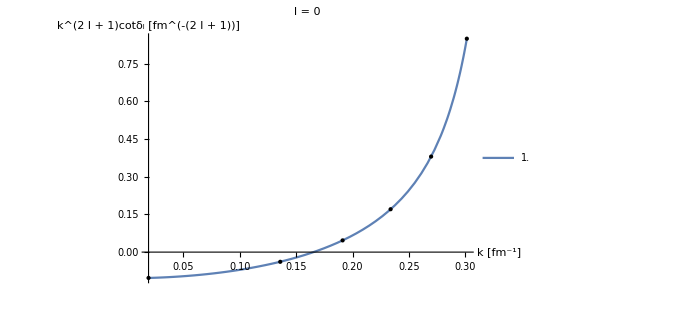

```mathematica
nn=9;
P2[mom_]:=modelX/.PadeSolus[[nn]][[2]]/.k->mom;
Plot[P2[kk],{kk,PrangeFM[[1]],PrangeFM[[-1]]},AxesLabel->{"k [fm^-1]","k^(2  l + 1)cotδ_l [fm^(-(2  l + 1))]"},ImageSize->500,PlotLegends->LEC[[All,1]],PlotRange->Full,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16],Epilog->Map[Point,data[[nn]]]]
```

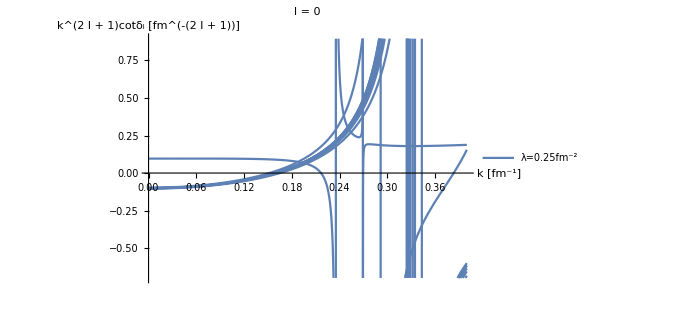

```mathematica
lgds="λ="<>ToString[0.25 #^2]<>"fm^-2"&/@LEC[[All,1]];
Plot[(modelX/.#[[2]]/.k->mom&/@PadeSolus),{mom,0,0.4},AxesLabel->{"k [fm^-1]","k^(2  l + 1)cotδ_l [fm^(-(2  l + 1))]"},ImageSize->500,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16],PlotLegends->lgds]
```

(1-3) neutron-triton (P-wave)

we chose the same α which yielded a singlet n-t value a_s≈9±2fm    
the momentum at which a_1is derived from -k^3cotδ is larger compared with the S-wave to reduce numerical complications associated with an extremely small denominator

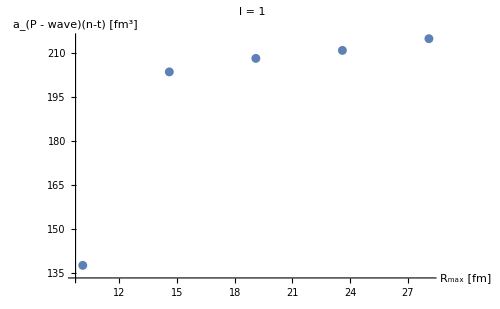

```mathematica
nGrid     =250;
ErangeMeV=(*{0.001};*)Range[0.01,3,0.5];
PrangeFM=(Sqrt[2 μ #]/hbar)&/@ErangeMeV;
Lrel=1;
a1fa={};
α0=0.066;
mom=0.001;
SetSharedVariable[aP];
aP={};
nn=Length[LEC]-2;
ParallelDo[
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,mom,Lrel,λ,C0,D0,α0]];
AppendTo[aP,{rr,-TanDelPwave/mom^(2 Lrel+1)}];
,{rr,Range[10.1,30.1,4.5]}];
a1=Reverse[Sort[aP,#1[[1]]>#2[[1]]&]];
AppendTo[a1fa,a1];

leg="α = "<>ToString[#]<>" fm^-2"&/@α0;
ListPlot[a1fa,AxesLabel->{"R_max [fm]","a_(P - wave)(n-t) [fm^3]"},ImageSize->500,PlotLegends->leg,PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
```

S-matrix pole (S-wave)

Kukulin, Theory of Resonances, ch.6.1.1 Eq.(1.1) ff      S_l(k)=Numerator/(k^(2l+1)cotδ_l-ik^(2l+1))      →_(k→0)        Numerator/(-a_l^-1+1/2 r_l k^2+O(k^4)-ik^(2l+1))
Pade (typeII): X_l(k)=(P_N^(l)(k^2))/(Q_M^(l)(k^2)):=k^(2l+1)cotδ_l  ⇒   S_l(k)=(P_N^(l)(k^2) + ik^(2l+1)Q_M^(l)(k^2))/(P_N^(l)(k^2) - ik^(2l+1)Q_M^(l)(k^2))    ⇒     P_N^(l)(k_res^2)-ik_res^(2l+1)Q_M^(l)(k_res^2)=0

```mathematica
nGrid     =250;
ErangeMeV=(*{0.001};*)Range[0.01,10,0.5];

Lrel=1;

α0=0.066;
nN=111;
Poles={};PadeSolus={};data={};
Do[
SetSharedVariable[Xl];
Xl={};
rr=20;
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];
ParallelDo[
momFM=Sqrt[2 μ En]/hbar;
TanDel=Chop[SolveSecular[rr,nGrid,momFM,Lrel,λ,C0,D0,α0]];
AppendTo[Xl,{En,(En^(Lrel+0.5))/TanDel}];
,{En,ErangeMeV}];
Xlr=Reverse[Sort[Xl,#1[[1]]>#2[[1]]&]];
AppendTo[data,Xlr];

PadeOrderN=3;PadeOrderM=2;
coffs={Array[cn,PadeOrderN+1],Array[cm,PadeOrderM+1]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{-1.01,1.2},Length[Flatten[coffs]]]}];
constr=10^1>#>-10^1&/@Flatten[coffs];

PadePolyP=Sum[coffs[[1]][[i+1]] ee^i,{i,0,PadeOrderN}];
PadePolyQ=Sum[coffs[[2]][[i+1]] ee^i,{i,0,PadeOrderM}];
modelX=PadePolyP/PadePolyQ;

solu=FindFit[Xlr,{modelX,constr},Flatten[coffs],ee,MaxIterations->500];

poles=Solve[((PadePolyP/PadePolyQ-I ee^(Lrel+0.5))/.solu)==0,ee];

Print["λ = ",λ,"   : E_pole = ",poles,"   ",solu];

AppendTo[Poles,Transpose[{Table[λ,Length[poles]],Flatten[ee/.poles]}]];
AppendTo[PadeSolus,{λ,solu}];
,{nn,Range[1,Min[nN+1,Length[LEC]]]}]
tmp=Transpose[{#[[1]]&/@Flatten[Poles,1],Re[#[[2]]]&/@Flatten[Poles,1],Im[#[[2]]]&/@Flatten[Poles,1]}];
Export[NotebookDirectory[]<>"pole_data_Pwave_31.dat",tmp,"Table","FieldSeparators"->"    "]
```

λ = 0.25   : E_pole = {{ee→-0.229397},{ee→1.28715+2.279 ⅈ},{ee→6.45386+5.95509 ⅈ}}   {cn[1]→-1.70741,cn[2]→-8.5714,cn[3]→1.71602,cn[4]→0.374863,cm[1]→3.48309,cm[2]→1.46582,cm[3]→-0.195295}

λ = 0.275625   : E_pole = {{ee→-0.181506},{ee→1.15523+1.99337 ⅈ},{ee→6.39604+5.73379 ⅈ}}   {cn[1]→-1.60483,cn[2]→-9.67374,cn[3]→1.1674,cn[4]→0.687984,cm[1]→2.906,cm[2]→2.74537,cm[3]→-0.323651}

λ = 0.3025   : E_pole = {{ee→-0.0880406},{ee→0.992153+1.7325 ⅈ},{ee→6.33175+5.55241 ⅈ}}   {cn[1]→-0.638075,cn[2]→-7.49539,cn[3]→-0.0533978,cn[4]→0.859253,cm[1]→1.10277,cm[2]→3.43893,cm[3]→-0.375742}

λ = 0.36   : E_pole = {{ee→-113.517},{ee→-0.517152-0.451416 ⅈ},{ee→-0.312622+0.841852 ⅈ},{ee→1.38215+0.869167 ⅈ}}   {cn[1]→8.9753,cn[2]→8.71547,cn[3]→6.43129,cn[4]→-9.51363,cm[1]→-8.88214,cm[2]→-7.02788,cm[3]→0.836961}

λ = 0.5625   : E_pole = {{ee→-2.0209},{ee→0.791438+2.07795 ⅈ},{ee→6.12101+5.86746 ⅈ}}   {cn[1]→8.53407,cn[2]→7.86217,cn[3]→-2.12314,cn[4]→-0.396804,cm[1]→-7.13651,cm[2]→-0.973981,cm[3]→0.178727}

λ = 1.   : E_pole = {{ee→-3.05616},{ee→0.613315+2.558 ⅈ},{ee→5.86015+6.43691 ⅈ}}   {cn[1]→7.87096,cn[2]→7.32076,cn[3]→-2.61968,cn[4]→-0.12184,cm[1]→-7.16237,cm[2]→0.0482153,cm[3]→0.0713655}

λ = 2.25   : E_pole = {{ee→-10.0533},{ee→0.1671+2.48288 ⅈ},{ee→5.27676+6.65911 ⅈ}}   {cn[1]→7.37242,cn[2]→6.28201,cn[3]→-2.60756,cn[4]→-0.00382713,cm[1]→-6.95002,cm[2]→0.505995,cm[3]→0.0211851}

λ = 4.   : E_pole = {{ee→-3.12541},{ee→-0.591868+3.4765 ⅈ},{ee→4.94858+7.00994 ⅈ}}   {cn[1]→5.92559,cn[2]→7.95232,cn[3]→-2.97379,cn[4]→-0.00120423,cm[1]→-7.36305,cm[2]→0.500698,cm[3]→0.0257459}

λ = 9.   : E_pole = {{ee→-43.2765},{ee→-0.631855+2.37525 ⅈ},{ee→4.39616+6.54219 ⅈ}}   {cn[1]→6.0038,cn[2]→6.80509,cn[3]→-2.79906,cn[4]→0.0515617,cm[1]→-6.99512,cm[2]→0.696809,cm[3]→0.00162551}

λ = 25.   : E_pole = {{ee→-63.7613+199.129 ⅈ},{ee→-0.839374+2.24551 ⅈ},{ee→4.22154+6.37904 ⅈ}}   {cn[1]→5.44802,cn[2]→6.66563,cn[3]→-2.72783,cn[4]→0.0599932,cm[1]→-6.73128,cm[2]→0.705317,cm[3]→-0.00215316}

λ = 49.   : E_pole = {{ee→-0.876592+2.18837 ⅈ},{ee→4.19405+6.31255 ⅈ},{ee→36.9902+127.255 ⅈ}}   {cn[1]→5.36554,cn[2]→6.69407,cn[3]→-2.73892,cn[4]→0.0633451,cm[1]→-6.74362,cm[2]→0.718692,cm[3]→-0.00345911}

/home/kirscher/kette_repo/AcoreNteraction/source_mathematica/pole_data_Pwave_31.dat

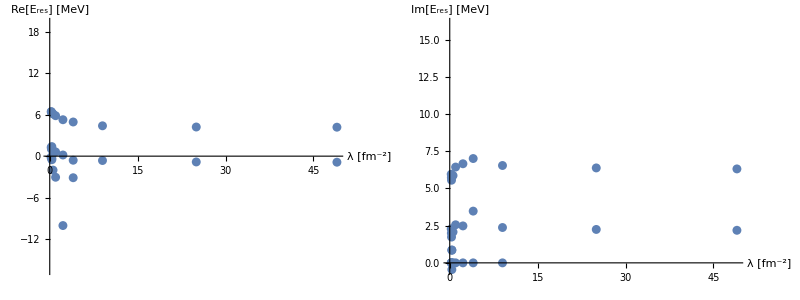

```mathematica
Poland=Transpose[{Flatten[Poles,1][[All,1]],Flatten[Poles,1][[All,2]]}];
PolandRe=Transpose[{Flatten[Poles,1][[All,1]],Re[Flatten[Poles,1][[All,2]]]}];
PolandIm=Transpose[{Flatten[Poles,1][[All,1]],Im[Flatten[Poles,1][[All,2]]]}];
Grid[{{ListPlot[PolandRe,AxesLabel->{"λ [fm^-2]","Re[E_res] [MeV]"},ImageSize->500],
ListPlot[PolandIm,AxesLabel->{"λ [fm^-2]","Im[E_res] [MeV]"},ImageSize->500]}}]
```

```mathematica
cplxpoles=Transpose[{Re[Poland[[All,2]]],Im[Poland[[All,2]]]}];
ListPlot[cplxpoles->Poland[[All,1]],PlotRange->Automatic,AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]
```

-Graphics-

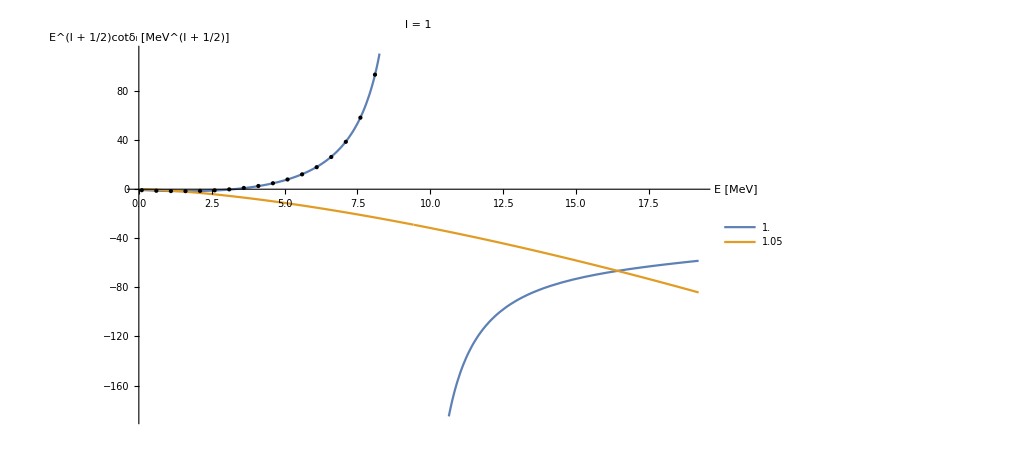

```mathematica
nn=2;
P2[Ee_]:=modelX/.PadeSolus[[nn]][[2]]/.ee->Ee;
Plot[{Re[P2[ee]-I ee^(Lrel+1./2.)],Im[P2[ee]-I ee^(Lrel+1./2.)]},{ee,ErangeMeV[[1]],2 ErangeMeV[[-1]]},AxesLabel->{"E [MeV]","E^(l + 1/2)cotδ_l [MeV^(l + 1/2)]"},ImageSize->750,PlotLegends->LEC[[All,1]],PlotRange->Automatic,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16],Epilog->{PointSize[Large],Map[Point,data[[nn]]]}]
```

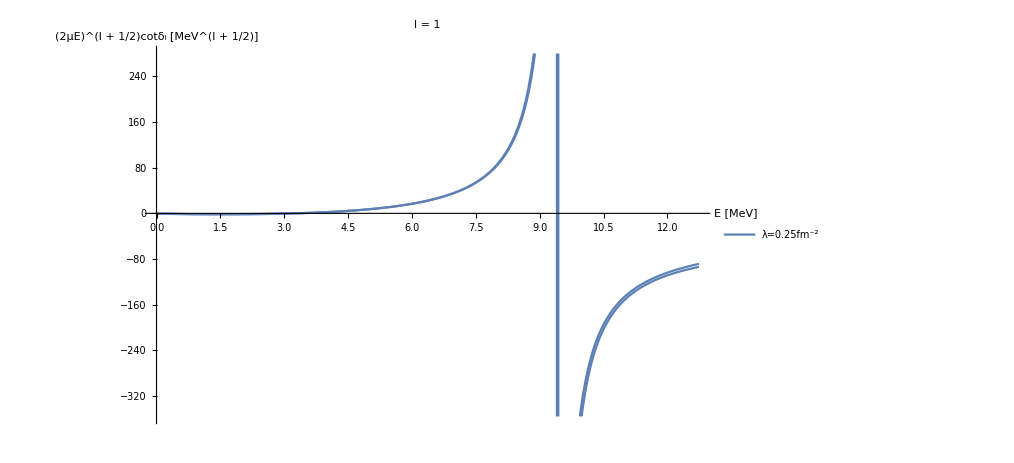

```mathematica
lgds="λ="<>ToString[0.25 #^2]<>"fm^-2"&/@LEC[[All,1]];
Plot[(modelX/.#[[2]]/.ee->En&/@PadeSolus),{En,0,12.74},AxesLabel->{"E [MeV]","(2μE)^(l + 1/2)cotδ_l [MeV^(l + 1/2)]"},ImageSize->750,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16],PlotLegends->lgds]
```